amplitude

707

zero - 1200Hz

59

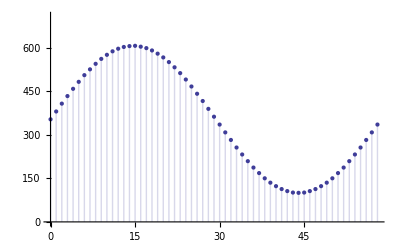

one - 2200Hz

32

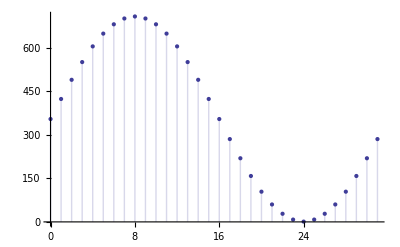

zero - 1200Hz

(353.
380.
407.
433.
458.
482.
505.
525.
544.
561.
575.
587.
596.
602.
605.
606.
603.
598.
590.
579.
566.
550.
532.
512.
490.
466.
441.
416.
389.
362.
335.
308.
282.
256.
232.
209.
187.
168.
150.
135.
123.
113.
106.
101.
100.
101.
106.
113.
123.
135.
150.
168.
187.
209.
232.
256.
282.
308.
335.)

one - 2200Hz

(354.
423.
489.
550.
604.
648.
680.
700.
707.
700.
680.
648.
604.
550.
489.
423.
354.
285.
219.
158.
104.
60.
28.
8.
1.
8.
28.
60.
104.
158.
219.
285.)

```mathematica
Clear["Global`*"]
samples:=32
amplitude:=707
halfAmplitude:=((amplitude-1)/2)
period1:=(2π)/samples
samplesCount1:=Round[(2π)/period1]-1
period0:=1200/2200 period1
samplesCount0:=Floor[(2π)/period0]
(* added pre-emphasis *)
f0[x_]:=Round[100+(halfAmplitude-100)(1+Sin[period0*x])]
f1[x_]:=Round[1+halfAmplitude(1+Sin[period1*x])]

"amplitude"
Round[amplitude]
"zero - 1200Hz"
samplesCount0 + 1
DiscretePlot[f0[x],{x,0,samplesCount0},PlotRange->{{0,samplesCount0},{0,amplitude}}]
"one - 2200Hz"
samplesCount1 + 1
DiscretePlot[f1[x],{x,0,samplesCount1},
PlotRange->{{0,samplesCount1},{0,amplitude}}]
"zero - 1200Hz"
MatrixForm[Table[N[f0[x]],{x,0,samplesCount0,1}]]
"one - 2200Hz"
MatrixForm[Table[N[f1[x]],{x,0,samplesCount1,1}]]
```